```mathematica
LinguisticAssistant
```

Missing[NoWolframParse,]

Gaussian Rays

-Graphics-

-Graphics-

```mathematica
w0 := (2 λ)/π F/d; (* {{F: focal length}, {d : inital beam radius}}*)
Zr := (π w0^2)/λ;(* {{w0: waist radius}, {λ: laser wavelength}} *)
Θ:=λ/(π w0)(* beam divergence in radians far away from the waist where 
divergence is linear *)
q[z_]:=(z - z0) + ⅈ Zr (* complex beam parameter, z0 is the location
of the beams waist *)
laserparams={
f -> 10000, (* laser frequency *)
λ -> 1300 10^-9,(* laser wave length *)
τ -> 150 10^-15 ,(* pulse length *)
P -> 10 10^-3,(* average laser power *)
F->50 10^-2,
d -> 2 10^-3,(* initial beam thickness *)
Imax -> 5 10^4 10 10^9,
τd->1/f
};

(*τd = 1/f; *)(* laser dead time = 100 μs *)
Wp=P*τd;
Pp=0.94*Wp/τ;
IPeak = (2 Pp)/(π w0^2);(* peak intensity  *)
IPeak2 = 2 Pp/(π d^2);(* no focusing *)
"Laser Peak intensity and doubled rayleigh range"
N@{IPeak2 τd 10^-4}//.laserparams
NSolve[IPeak ==Imax,F]//.laserparams
```

Laser Peak intensity and doubled rayleigh range

{9973.71}

{{1/2→-0.215864},{1/2→0.215864}}

## Fitting a gaussian beam

```mathematica
D[Erfc[(x-x0)/(√2 w)],x]
```

-(ⅇ^(-(x-x0)^2/(2 w^2)) √(2/π))/w

```mathematica
gaussian[x_,a_,b_,x0_]:=a ⅇ^(-b (x-x0)^2)
erfc[x_,a_,w_,x0_,c_]:=a Erfc[(x-x0)/(2w)]+c
fitGaussian[data_]:=FindFit[data,gaussian[x,a,b,x0],{a,b,x0},x]
fitErfc[data_]:=FindFit[data,erfc[x,a,w,x0,c],{a,w,x0,c},x]
```

{a→6.73707,w→6.29677,x0→-12.1061,c→-10.4791}

{1,6.29677}

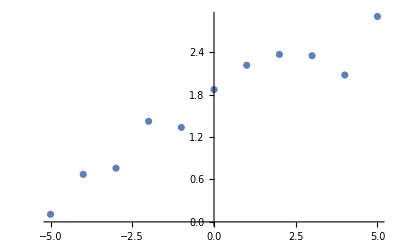
{1,6.29677,-Graphics-}

```mathematica
sample ={ 1,#, erfc[#,1,2,0]+RandomReal[1]}&/@Range[-5,5,1];
(*Import["~/bachelor/measurements/gaussian_divergence_example.csv"]*)fitErfc[sample[[All,2;;3]]]
fwhmAtZ[sample_]:=({sample[[1,1]],w}
/.fitErfc[sample[[All,2;;3]]]
(*fwhm->2 √(Log[2]/b)]*))
divAngleAndWaistLocation[sample_]:={Θ-> ArcTan[a]z0-> -b/a}/.FindFit[
fwhmAtZ/@GatherBy[sample,First]
,a x + b, {a,b},x]

plotFitAtZ[sample_]:=
{sample[[1,1]],
w/.fitErfc[sample[[All,2;;3]]],
Show[{
ListPlot[sample[[All,2;;3]]],Plot[Evaluate[erfc[x,a,w,x0]/.fitErfc[sample[[All,2;;3]]],{x,-5,5},PlotRange->Full]]
}]
}


fwhmAtZ[sample]
plotFitAtZ[sample]
```

{d/(2 F)→0.803889 z0→0.0729731}

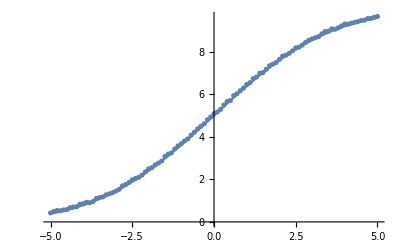
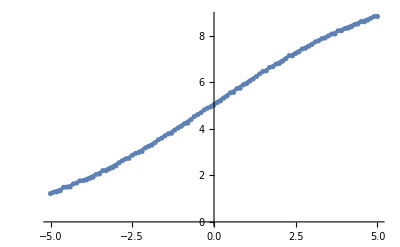
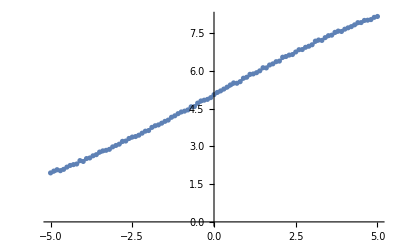
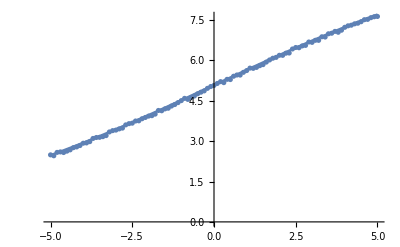
{{2,1.99619,-Graphics-},{3,3.05364,-Graphics-},{4,4.05273,-Graphics-},{5,5.1221,-Graphics-}}

```mathematica
sample =Tuples[{Range[2,5,1],Range[-5,5,.1]}]/.{z_,y_}:>{z ,y, erfc[y,5,z,0]+RandomReal[.1]};

(*dataps=ListPlot/@GatherBy[sample,First][[All,All,2;;3]]*)(*
div=fwhmAtZ/@GatherBy[sample,First]*)

divAngleAndWaistLocation[sample]
plotFitAtZ/@GatherBy[sample,First]
```

```mathematica
data = Import["./measurements/10_razorblade_40mm_x.csv"][[2;;]];
```

{d/(2 F)→-0.0198384 z0→7.17788}

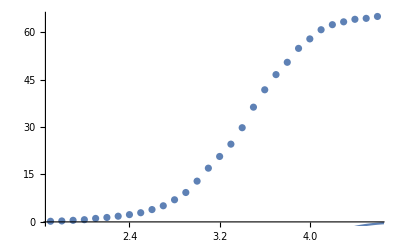
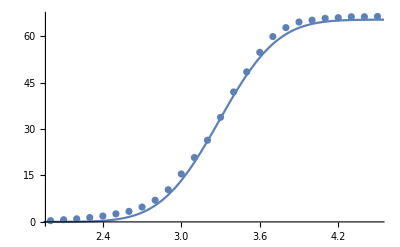
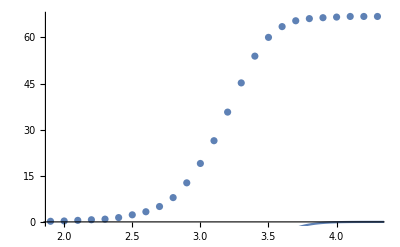
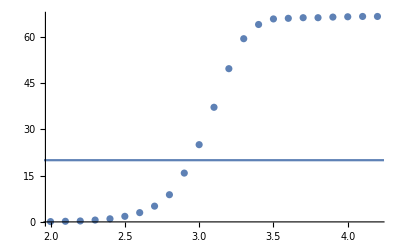
{{10,-0.342837,-Graphics-},{15,0.247707,-Graphics-},{20,-0.199685,-Graphics-},{25,-0.524389,-Graphics-}}

```mathematica
divAngleAndWaistLocation[data]
plotFitAtZ/@GatherBy[data,First]
```